```mathematica
matrices = Partition[#,3]&/@Permutations[Range[9]];
determinants = Abs[Det[#]]&/@matrices;
```

1.)

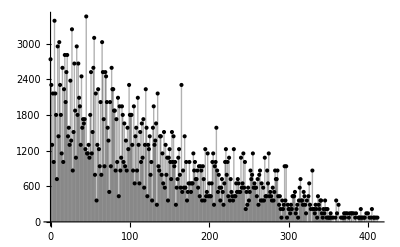

```mathematica
ListPlot[
Tally[
determinants
],
Filling->Bottom,
PlotStyle->Black
]
```

2.)

a.)

```mathematica
Max[determinants]
```

412

b.)

```mathematica
Commonest[determinants]
```

{45}

c.)

```mathematica
N[Mean[determinants],6]
```

123.211

d.)

```mathematica
Median[determinants]
```

101

e.)

```mathematica
Count[
Map[
PrimeQ[#]&,
determinants
],
True
]
```

77112

f.)

```mathematica
Count[
Map[
EvenQ[#]&,
determinants
],
True
]>
Count[
Map[
OddQ[#]&,
determinants
],
True
]
```

False

There are more odd determinants because the output is false when you set the number of evens greater than the number of odds.

g.)

```mathematica
Commonest@Select[
Flatten[
Map[
Divisors[#]&,
determinants
]
],
#>1&
]
```

{2}

3.)

```mathematica
TableForm[
Partition[
Map[
MatrixForm[#]&,
Select[matrices,Abs@Det[#]==298&]
],
8
],
TableSpacing->{1.3,1}
]
```

(1 | 4 | 7
6 | 8 | 5
9 | 2 | 3) | (1 | 4 | 7
9 | 2 | 3
6 | 8 | 5) | (1 | 6 | 9
4 | 8 | 2
7 | 5 | 3) | (1 | 6 | 9
7 | 5 | 3
4 | 8 | 2) | (1 | 7 | 4
6 | 5 | 8
9 | 3 | 2) | (1 | 7 | 4
9 | 3 | 2
6 | 5 | 8) | (1 | 9 | 6
4 | 2 | 8
7 | 3 | 5) | (1 | 9 | 6
7 | 3 | 5
4 | 2 | 8)
(2 | 3 | 9
4 | 7 | 1
8 | 5 | 6) | (2 | 3 | 9
8 | 5 | 6
4 | 7 | 1) | (2 | 4 | 8
3 | 7 | 5
9 | 1 | 6) | (2 | 4 | 8
9 | 1 | 6
3 | 7 | 5) | (2 | 8 | 4
3 | 5 | 7
9 | 6 | 1) | (2 | 8 | 4
9 | 6 | 1
3 | 5 | 7) | (2 | 9 | 3
4 | 1 | 7
8 | 6 | 5) | (2 | 9 | 3
8 | 6 | 5
4 | 1 | 7)
(3 | 2 | 9
5 | 8 | 6
7 | 4 | 1) | (3 | 2 | 9
7 | 4 | 1
5 | 8 | 6) | (3 | 5 | 7
2 | 8 | 4
9 | 6 | 1) | (3 | 5 | 7
9 | 6 | 1
2 | 8 | 4) | (3 | 7 | 5
2 | 4 | 8
9 | 1 | 6) | (3 | 7 | 5
9 | 1 | 6
2 | 4 | 8) | (3 | 9 | 2
5 | 6 | 8
7 | 1 | 4) | (3 | 9 | 2
7 | 1 | 4
5 | 6 | 8)
(4 | 1 | 7
2 | 9 | 3
8 | 6 | 5) | (4 | 1 | 7
8 | 6 | 5
2 | 9 | 3) | (4 | 2 | 8
1 | 9 | 6
7 | 3 | 5) | (4 | 2 | 8
7 | 3 | 5
1 | 9 | 6) | (4 | 7 | 1
2 | 3 | 9
8 | 5 | 6) | (4 | 7 | 1
8 | 5 | 6
2 | 3 | 9) | (4 | 8 | 2
1 | 6 | 9
7 | 5 | 3) | (4 | 8 | 2
7 | 5 | 3
1 | 6 | 9)
(5 | 3 | 7
6 | 9 | 1
8 | 2 | 4) | (5 | 3 | 7
8 | 2 | 4
6 | 9 | 1) | (5 | 6 | 8
3 | 9 | 2
7 | 1 | 4) | (5 | 6 | 8
7 | 1 | 4
3 | 9 | 2) | (5 | 7 | 3
6 | 1 | 9
8 | 4 | 2) | (5 | 7 | 3
8 | 4 | 2
6 | 1 | 9) | (5 | 8 | 6
3 | 2 | 9
7 | 4 | 1) | (5 | 8 | 6
7 | 4 | 1
3 | 2 | 9)
(6 | 1 | 9
5 | 7 | 3
8 | 4 | 2) | (6 | 1 | 9
8 | 4 | 2
5 | 7 | 3) | (6 | 5 | 8
1 | 7 | 4
9 | 3 | 2) | (6 | 5 | 8
9 | 3 | 2
1 | 7 | 4) | (6 | 8 | 5
1 | 4 | 7
9 | 2 | 3) | (6 | 8 | 5
9 | 2 | 3
1 | 4 | 7) | (6 | 9 | 1
5 | 3 | 7
8 | 2 | 4) | (6 | 9 | 1
8 | 2 | 4
5 | 3 | 7)
(7 | 1 | 4
3 | 9 | 2
5 | 6 | 8) | (7 | 1 | 4
5 | 6 | 8
3 | 9 | 2) | (7 | 3 | 5
1 | 9 | 6
4 | 2 | 8) | (7 | 3 | 5
4 | 2 | 8
1 | 9 | 6) | (7 | 4 | 1
3 | 2 | 9
5 | 8 | 6) | (7 | 4 | 1
5 | 8 | 6
3 | 2 | 9) | (7 | 5 | 3
1 | 6 | 9
4 | 8 | 2) | (7 | 5 | 3
4 | 8 | 2
1 | 6 | 9)
(8 | 2 | 4
5 | 3 | 7
6 | 9 | 1) | (8 | 2 | 4
6 | 9 | 1
5 | 3 | 7) | (8 | 4 | 2
5 | 7 | 3
6 | 1 | 9) | (8 | 4 | 2
6 | 1 | 9
5 | 7 | 3) | (8 | 5 | 6
2 | 3 | 9
4 | 7 | 1) | (8 | 5 | 6
4 | 7 | 1
2 | 3 | 9) | (8 | 6 | 5
2 | 9 | 3
4 | 1 | 7) | (8 | 6 | 5
4 | 1 | 7
2 | 9 | 3)
(9 | 1 | 6
2 | 4 | 8
3 | 7 | 5) | (9 | 1 | 6
3 | 7 | 5
2 | 4 | 8) | (9 | 2 | 3
1 | 4 | 7
6 | 8 | 5) | (9 | 2 | 3
6 | 8 | 5
1 | 4 | 7) | (9 | 3 | 2
1 | 7 | 4
6 | 5 | 8) | (9 | 3 | 2
6 | 5 | 8
1 | 7 | 4) | (9 | 6 | 1
2 | 8 | 4
3 | 5 | 7) | (9 | 6 | 1
3 | 5 | 7
2 | 8 | 4)

4.)

```mathematica
#[[2]]&/@Tally[
Select[
Flatten[
Map[
Divisors[#]&,
determinants
]
],
#>1&& #<18&
]
]
```

{142416,51696,49680,94032,35712,31392,152784,73296,64368,28944,44640,41616,19440,22968,33552,15696}

```mathematica
PieChart[#[[2]]&/@SortBy[
Tally[
Select[
Flatten[
Map[
Divisors[#]&,
determinants
]
],
#>1&& #<18&
]
],
First
],
ChartLabels->{Range[2,17,1]}
]
```

-Graphics-